```mathematica
Needs["NDSolve`FEM`"]
```

Generate mesh for a beam with a crack inside at given position.

```mathematica
generateMesh[crackX_, crackY_, crackExtent_] := Module[{Ω, mesh},Ω = RegionDifference[Rectangle[{0,0},{200,20}],Ellipsoid[{crackX,crackY}, {crackExtent,2}]];
mesh=ToElementMesh[Ω, MaxCellMeasure->20];
Return[mesh];]
```

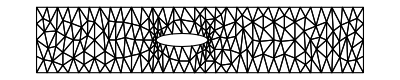

```mathematica
generateMesh[89, 10, 16];
%["Wireframe"]
```

Define operator and boundary conditions.

```mathematica
op={({{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive}/.{Y->12.7 10^4,ν->33/100};
```

```mathematica
Subscript[Γ, D]=DirichletCondition[{u[x,y]==0.,v[x,y]==0.},x==0];
```

Solve PDE for a given mesh.

```mathematica
solvePDE[mesh_]:=NDSolveValue[{op=={0,NeumannValue[-20,x==200]},Subscript[Γ, D]},{u,v},{x, y}∈mesh];
```

Show pictures for given mesh and solution.

```mathematica
showPic[mesh_, sol_]:=Show[{mesh["Wireframe"["MeshElement"-> "BoundaryElements"]],
ElementMeshDeformation[mesh, sol]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]}];
showDiagram[mesh_,sol_]:=ContourPlot[sol[[1]][x,y], {x, y}∈mesh, ColorFunction->"Temperature", AspectRatio->Automatic]
```

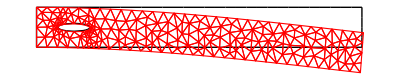

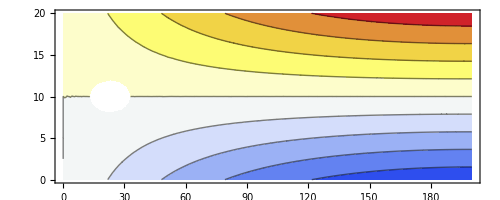

```mathematica
m=generateMesh[23, 10, 10];
sol=solvePDE[m];
showPic[m,sol]
showDiagram[m,sol]
```

Print and export sensors readings.

```mathematica
points = Table[{x, sol[[1]][x, 20]}, {x, Range[0, 200, 20]}]
```

{{0,0.},{20,0.184556},{40,0.340385},{60,0.481999},{80,0.60483},{100,0.708774},{120,0.793812},{140,0.859956},{160,0.907198},{180,0.935537},{200,0.945529}}

```mathematica
If[!DirectoryQ["Mathematica_Export"], CreateDirectory["Mathematica_Export"]]
```

/Users/admishchenko/Mathematica_Export

```mathematica
Export["~/Mathematica_Export/test.txt", points, "Table"]
```

~/Mathematica_Export/test.txt

Export sensors readings in the cycle.

```mathematica
n = 10000;
i = 0;

If[FileExistsQ["~/Mathematica_Export/output.txt"], DeleteFile["~/Mathematica_Export/output.txt"]]
str = File[CreateFile["~/Mathematica_Export/output.txt"]]
WriteString[str, "exp_number crackX crackY crackExtent sensor0 sensor1 sensor2 sensor3 sensor4 sensor5 sensor6 sensor7 sensor8 sensor9 sensor10\n"];

While[i<n,{
crackExtent=4+RandomReal[{0,12}];
crackX=crackExtent+ RandomReal[{0, 200-crackExtent*2}];
crackY = 2 + RandomReal[{0, 16}];
m=generateMesh[crackX,crackY,crackExtent];
sol=solvePDE[m];

skip=False;
sensorsList={};
For[j=0,j≤200,j+=20,{
sensor=sol[[1]][j,20];
If[sensor===Indeterminate,{
skip=True;
Break[];
},
sensorsList=Append[sensorsList,NumberForm[sensor,16]];
]
}];

If[skip==False,{
row=StringRiffle[{i,crackX,crackY,crackExtent}]<>" "<>StringRiffle[sensorsList] <> "\n";
WriteString[str,row];
i++;
If[Mod[i,100]==0,{Print[i]}]
}];
}]
Close[str]
```

File[/Users/admishchenko/Mathematica_Export/output.txt]

100

200

300

400

500

600

700

800

900

1000

1100

InterpolatingFunction::femdmval: Input value {160.,20.} lies outside the range of data in the interpolating function.

1200

1300

1400

1500

1600

1700

1800

1900

2000

2100

2200

2300

InterpolatingFunction::femdmval: Input value {120.,20.} lies outside the range of data in the interpolating function.

2400

2500

2600

2700

2800

2900

3000

3100

3200

3300

3400

InterpolatingFunction::femdmval: Input value {180.,20.} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

3500

3600

3700

3800

3900

4000

4100

4200

4300

4400

4500

4600

4700

4800

4900

5000

5100

5200

5300

5400

5500

5600

5700

5800

5900

6000

6100

6200

6300

6400

6500

6600

6700

6800

6900

7000

7100

7200

7300

7400

7500

7600

7700

7800

7900

8000

8100

8200

8300

8400

8500

8600

8700

8800

8900

9000

9100

9200

9300

9400

9500

9600

9700

9800

9900

10000

/Users/admishchenko/Mathematica_Export/output.txt